```mathematica
c2=0.54;
c1=1.4;
Dc=0.76;
Fc=0.5;
fc=0.093;
```

```mathematica
ap1=(-I)*(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
mpd=I*(-2*0.76)^2/(6*2*(0.093)^2*(2Pi)^4);
mpu=I*(-2*0.76)^2/(2*2*(0.093)^2*(2Pi)^4);
dp1=(-I)*(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
ep1=(-I)*(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
fp1=(I)*(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
gp1=(I)*(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
rsp1d=(-I)*(-2*0.76)^2/(6*2*(0.093)^2*(2Pi)^4);
rsp1u=(-I)*(-2*0.76)^2/(2*2*(0.093)^2*(2Pi)^4);
tup1d=(-I)*(-2*0.76)^2/(6*2*(0.093)^2*(2Pi)^4);
tup1u=(-I)*(-2*0.76)^2/(2*2*(0.093)^2*(2Pi)^4);
```

```mathematica
ap0=(-I)*(0.76+0.5)^2/(2*8*(0.093)^2*(2Pi)^4);
dp0=(-I)*(0.76+0.5)^2/(2*8*(0.093)^2*(2Pi)^4);
ep0=(-I)*(0.76+0.5)^2/(2*8*(0.093)^2*(2Pi)^4);
fp0=(I)*(0.76+0.5)^2/(2*8*(0.093)^2*(2Pi)^4);
gp0=(I)*(0.76+0.5)^2/(2*8*(0.093)^2*(2Pi)^4);
mp0=I*(-2*0.76)^2/(3*2*2*(0.093)^2*(2Pi)^4);
rsp0=(-I)*(-2*0.76)^2/(3*2*2*(0.093)^2*(2Pi)^4);
tup0=(-I)*(-2*0.76)^2/(3*2*2*(0.093)^2*(2Pi)^4);
```

```mathematica
a=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-a-L1-zero.wdx"];
f1na=Query[1]@a;
lf1na=Interpolation[Flatten[f1na,1]];
sf1a[x_,t_]=lf1na[x,t];

g1na=Query[2]@a;
lg1na=Interpolation[Flatten[g1na,1]];
sg1a[x_,t_]=lg1na[x,t];
d=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-d-L1-zero.wdx"];
f1nd=Query[1]@d;
lf1nd=Interpolation[Flatten[f1nd,1]];
sf1d[x_,t_]=lf1nd[x,t];

g1nd=Query[2]@d;
e=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-e-L1-zero.wdx"];
f1ne=Query[1]@e;
lf1ne=Interpolation[Flatten[f1ne,1]];
sf1e[x_,t_]=lf1ne[x,t];

g1ne=Query[2]@e;

f=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-f-L1-zero.wdx"];
f1nf=Query[1]@f;
lf1nf=Interpolation[Flatten[f1nf,1]];
sf1f[x_,t_]=lf1nf[x,t];

g1nf=Query[2]@f;
lg1nf=Interpolation[Flatten[g1nf,1]];
sg1f[x_,t_]=lg1nf[x,t];
g=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-g-L1-zero.wdx"];
f1ng=Query[1]@g;
lf1ng=Interpolation[Flatten[f1ng,1]];
sf1g[x_,t_]=lf1ng[x,t];

g1ng=Query[2]@g;
lg1ng=Interpolation[Flatten[g1ng,1]];
sg1g[x_,t_]=lg1ng[x,t];
m=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-m-L1-zero.wdx"];
f1nm=Query[1]@m;
lf1nm=Interpolation[Flatten[f1nm,1]];
sf1m[x_,t_]=lf1nm[x,t];

g1nm=Query[2]@m;
lg1nm=Interpolation[Flatten[g1nm,1]];
sg1m[x_,t_]=lg1nm[x,t];
rs=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-rs-L1-zero.wdx"];
f1nrs=Query[1]@rs;
lf1nrs=Interpolation[Flatten[f1nrs,1]];
sf1rs[x_,t_]=lf1nrs[x,t];

g1nrs=Query[2]@rs;
lg1nrs=Interpolation[Flatten[g1nrs,1]];
sg1rs[x_,t_]=lg1nrs[x,t];

tu=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-tu-L1-zero.wdx"];
f1ntu=Query[1]@tu;
lf1ntu=Interpolation[Flatten[f1ntu,1]];
sf1tu[x_,t_]=lf1ntu[x,t];

g1ntu=Query[2]@tu;
lg1ntu=Interpolation[Flatten[g1ntu,1]];
sg1tu[x_,t_]=lg1ntu[x,t];
```

```mathematica
(*pi+ channel*)
```

```mathematica
tfaz[x_,t_]=ap1*sf1a[x,t];
tgaz[x_,t_]=ap1*sg1a[x,t];
tfdez[x_,t_]=dp1*sf1d[x,t]+ep1*sf1e[x,t];
tffgz[x_,t_]=fp1*sf1f[x,t]+gp1*sf1g[x,t];
tgfgz[x_,t_]=fp1*sg1f[x,t]+gp1*sg1g[x,t];
tfrsz[x_,t_]=rsp1d*sf1rs[x,t];
tgrsz[x_,t_]=rsp1d*sg1rs[x,t];tftuz[x_,t_]=tup1d*sf1tu[x,t];
tgtuz[x_,t_]=tup1d*sg1tu[x,t];
```

```mathematica
(*pi0 channel*)
```

```mathematica
tfa0[x_,t_]=ap0*sf1a[x,t];
tga0[x_,t_]=ap0*sg1a[x,t];
tfde0[x_,t_]=dp0*sf1d[x,t]+ep0*sf1e[x,t];
tffg0[x_,t_]=fp0*sf1f[x,t]+gp0*sf1g[x,t];
tgfg0[x_,t_]=fp0*sg1f[x,t]+gp0*sg1g[x,t];
tfrs0[x_,t_]=rsp0*sf1rs[x,t];
tgrs0[x_,t_]=rsp0*sg1rs[x,t];tftu0[x_,t_]=tup0*sf1tu[x,t];
tgtu0[x_,t_]=tup0*sg1tu[x,t];
```

```mathematica
(*pi- channel*)
```

```mathematica
tfrsf[x_,t_]=rsp1u*sf1rs[x,t];
tgrsf[x_,t_]=rsp1u*sg1rs[x,t];tftuf[x_,t_]=tup1u*sf1tu[x,t];
tgtuf[x_,t_]=tup1u*sg1tu[x,t];
```

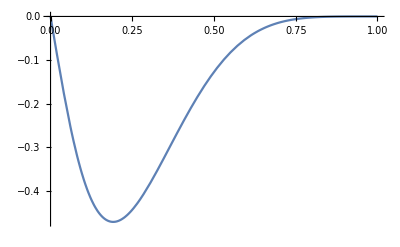

```mathematica
Plot[tfdez[x,0],{x,0,1}]
```

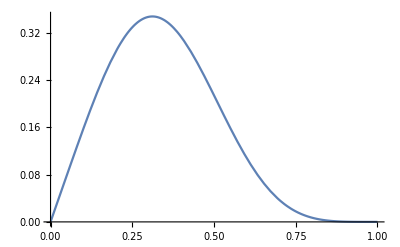

```mathematica
Plot[tffgz[x,0],{x,0,1}]
```

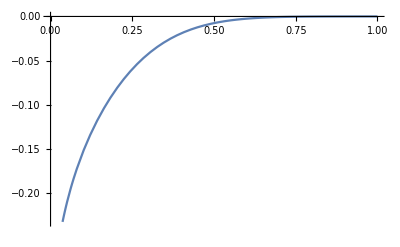

```mathematica
Plot[tfrsz[x,0],{x,0,1}]
```

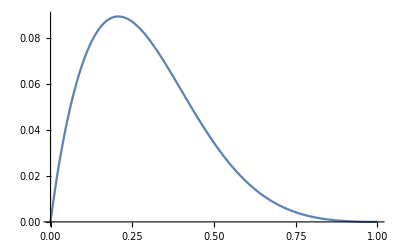

```mathematica
Plot[tftuz[x,0],{x,0,1}]
```

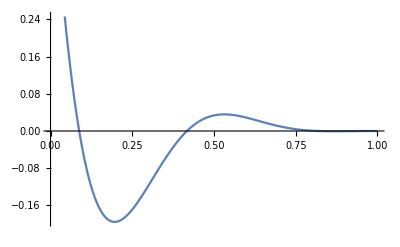

```mathematica
Plot[tfdez[x,0]+tffgz[x,0]+tfrsz[x,0]+tftuz[x,0]-(tfrsf[x,0]+tftuf[x,0]),{x,0,1}]
```